## Coupled oscillators (convert to network representation) Figure 14.3

```mathematica
Clear["Global`*"];
```

```mathematica
eqs={x''[t]+x[t]-y[t]==u[t],  y''[t]+y[t]-x[t]==0};
sys=StateSpaceModel[eqs,{x[t],x'[t],y[t],y'[t]},u[t],{x[t],y[t]},t]
```

01000-101010001010-1001000000100StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3$CellContext`stname4Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1241FalseFalseFalseAutomaticNone,{{x[t],0},x_1,{y[t],0},x_2},{{u[t],0}},Automatic,t

```mathematica
{a,b,c,d}=Normal[sys]; {MatrixForm[a],MatrixForm[b]}
```

{(0 | 1 | 0 | 0
-1 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | -1 | 0),(0
1
0
0)}

```mathematica
Wc=ControllabilityMatrix[sys]; MatrixForm[Wc]
```

(0 | 1 | 0 | -1
1 | 0 | -1 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0)

```mathematica
MatrixRank[Wc]
```

4

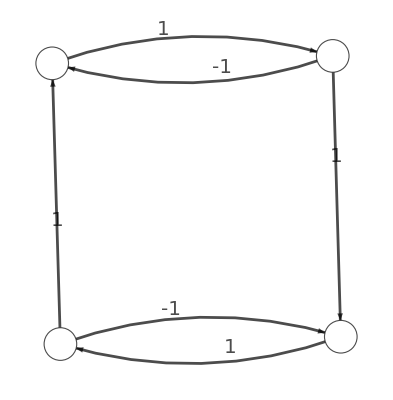

```mathematica
WeightedAdjacencyGraph[a/. 0->∞,VertexLabels->Placed["Name",Center],VertexStyle->White,VertexSize->{"Scaled", 0.08},VertexLabelStyle->Directive[FontFamily->"Gill Sans",20],EdgeStyle->Directive[Black,Thickness[0.005],Background->White],EdgeLabels->Placed["EdgeWeight",0.4],EdgeLabelStyle->Directive[FontFamily->"Gill Sans",20]]
```

```mathematica
Eigenvalues[a]//MatrixForm  (* "breather" mode and free translation *)
```

(ⅈ √2
-ⅈ √2
0
0)